### Start choosing the example:

```mathematica
t="Jamaratv9";
beta =0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t];
```

### Look at the output bellow before trying to rerun!

```mathematica
(*With U2->2, agents don't exit through 6. running with U2->U2 to determine the largest value for which we get some current, hence unicity.*)
```

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1-> 20,I2->200000, U1-> 200,U2->100,U3->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

Finished with the us!

Finish with the js

{0.19258,<|u1→10807580/41,u2→13807180/41,u3→10807580/41,u4→7807160/41,u5→13807180/41,u6→8606780/41,u7→7807160/41,u8→8606780/41,u9→7807160/41,u10→4007120/41,u11→8606780/41,u12→4206000/41,u13→4007120/41,u14→4206000/41,u15→4007120/41,u16→200,u17→4206000/41,u18→100,u19→200,u20→0,u21→200,u22→200,u23→100,u24→0,u25→100,u26→100,u27→0,u28→0,u29→10807580/41,u30→10807580/41,u31→13807180/41,u32→13807180/41,j21→0,j22→3990720/41,j25→0,j26→4197800/41,j27→0,j28→300,j29→0,j30→20,j31→0,j32→200000,j12→4400780/41,j14→0,j16→3998920/41,j18→4201900/41,j2→0,j20→200,j24→100,j4→3000420/41,j6→5200400/41,j8→0,j9→0,j1→2999600/41,j3→0,j5→0,j7→799620/41,j10→3800040/41,j11→0,j13→198880/41,j15→0,j17→0,j19→0,j23→0|>}

```mathematica
uvars=d2e["uvars"];
us=Values@uvars;
jvars=d2e["jvars"];
js=Values@jvars;
jtvars=d2e["jtvars"];
jts=Values@jtvars;
```

### Quest for subsystems!

#### how to find variables in some expressions of the system

```mathematica
getVar::usage ="getVar[exp] returns the variables in exp"
getVar[xp_And]:=getVar/@List@@xp//Flatten//DeleteDuplicates
getVar[GreaterEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[Equal[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[LessEqual[xp1_,xp2_]]:= Variables/@{xp1,xp2}//Flatten
getVar[xp_Or]:=getVar/@List@@xp//Flatten
```

```mathematica
colapse[{xp1_,xp2_}]:=
Which[SubsetQ[xp1,xp2],
xp1,
SubsetQ[xp2,xp1] ,
xp2,
True,
{xp1,xp2}
]
```

```mathematica
SimpleCrit[{{True,rules_}, critus_}]:={{True,rules},critus}
SimpleCrit[{{syscrit_,rules_},{}}]:=
Module[{subsol, newcrit= Simplify/@syscrit},
subsol = First@Solve[newcrit];
{{newcrit/.subsol,Join[rules,Association[subsol]]/.subsol}, {}}
]

SimpleCrit[{{syscrit_,rules_},critus_}]:=
Module[{var,subsys,subsol, newcrit = Simplify/@syscrit},
var=First[critus];
subsys=Select[newcrit, Function[xp, !FreeQ[var][xp]]];
If[subsys===True,
Return[{{newcrit,rules}, Rest[critus]}]
];
subsol=First@Solve[subsys[[1]],var];
{{syscrit/.subsol,Join[rules,Association[subsol]]/.subsol},Rest[critus]}
]
```

```mathematica
({sys,rules}=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

EliminateVarsSimplify for the us

u1≥u29&&u31≤49990+jt14/4+jt16/4-jt17/4-jt18/4+u1&&200020-5 jt14-5 jt16+5 jt17+5 jt18+u1≤200&&-750090+(21 jt14)/4+(21 jt16)/4-(21 jt17)/4-(21 jt18)/4+u1≤100&&-1200140+9 jt14+9 jt16-9 jt17-9 jt18+jt32+jt34-jt43+jt46+u1≤0&&(50010-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4-jt18/4+jt19+jt20==0||u1-u29==0)&&(-49990+jt12+jt13+(3 jt14)/4-jt16/4+jt17/4+jt18/4-jt19-jt20==0||u1-u29==0)&&(200000-jt12==0||49990+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt12==0||49990+jt14/4+jt16/4-jt17/4-jt18/4+u1-u31==0)&&(jt14+jt16-jt25+jt28-jt37==0||-199820+5 jt14+5 jt16-5 jt17-5 jt18-u1==0)&&(-1650190+(67 jt14)/4+(67 jt16)/4-(71 jt17)/4-(71 jt18)/4+jt25-jt28+jt32+jt34+jt37-jt43+jt46==0||-199820+5 jt14+5 jt16-5 jt17-5 jt18-u1==0)&&(jt32+jt34-jt43==0||750190-(21 jt14)/4-(21 jt16)/4+(21 jt17)/4+(21 jt18)/4-u1==0)&&(jt46==0||750190-(21 jt14)/4-(21 jt16)/4+(21 jt17)/4+(21 jt18)/4-u1==0)&&(450050-(15 jt14)/4-(15 jt16)/4+(15 jt17)/4+(15 jt18)/4-jt32-jt34+jt37-jt46==0||1200140-9 jt14-9 jt16+9 jt17+9 jt18-jt32-jt34+jt43-jt46-u1==0)&&(1400160-14 jt14-14 jt16+14 jt17+14 jt18-jt32-jt34-jt37+2 jt43-jt46==0||1200140-9 jt14-9 jt16+9 jt17+9 jt18-jt32-jt34+jt43-jt46-u1==0)

Reducing ...

Reducing again ...

Clean equalities for system of u1

Finished with the us!

Finish with the js

{0.071617,{49990-jt12+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20≥0&&-jt12+jt19+jt20≥0&&-50010+jt13+(3 jt14)/4-jt16/4+1/4 (-3800040/41+jt14+jt16-jt17)+jt17/4≥0&&jt13+jt14≥0&&-150010+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20≥0&&jt19+jt20≥0&&-50010+jt13+(3 jt14)/4+(3 jt16)/4+1/4 (-3800040/41+jt14+jt16-jt17)-(3 jt17)/4≥0&&-3800040/41+jt13+jt14+jt16-jt17≥0&&-3800040/41+jt14+jt16≥0&&jt14+jt16≥0&&-4400780/41+jt20+jt22≥0&&jt20+jt22≥0&&-3800040/41+jt14+jt16+jt28-jt29≥0&&250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4+jt28-jt29≥0&&250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4-jt25+jt28≥0&&jt14+jt16-jt25+jt28≥0&&-450050+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt32+jt34≥0&&jt32+jt34≥0&&-53208760/41+14 jt14+14 jt16-14 (-3800040/41+jt14+jt16-jt17)-14 jt17+jt37≥0&&jt37≥0&&-63459990/41+(71 jt14)/4+(71 jt16)/4-71/4 (-3800040/41+jt14+jt16-jt17)-(71 jt17)/4≥0&&-14254250/41+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt43≥0&&jt43≥0&&1850210-(71 jt14)/4-(71 jt16)/4+71/4 (-3800040/41+jt14+jt16-jt17)+(71 jt17)/4-2 jt32-2 jt34+2 jt43-2 (4197800/41-jt32-jt34+jt43)≥0&&49990-jt12+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20≥0&&-50010+jt13+(3 jt14)/4-jt16/4+1/4 (-3800040/41+jt14+jt16-jt17)+jt17/4≥0&&50010-jt12-jt13-(3 jt14)/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20≥0&&-49990+jt12+jt13+(3 jt14)/4-jt16/4+1/4 (-3800040/41+jt14+jt16-jt17)+jt17/4-jt19-jt20≥0&&-jt12+jt19+jt20≥0&&-150010+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20≥0&&200000-jt12≥0&&jt12≥0&&jt13≥0&&jt14≥0&&-50010+jt13+(3 jt14)/4-jt16/4+1/4 (-3800040/41+jt14+jt16-jt17)-(3 jt17)/4≥0&&jt16≥0&&jt17≥0&&-3800040/41+jt14+jt16-jt17≥0&&jt19≥0&&jt20≥0&&-3800040/41+jt13+jt14+jt16-jt17-jt22≥0&&jt22≥0&&-150010-jt13+jt14/4+jt16/4-5/4 (-3800040/41+jt14+jt16-jt17)-jt17/4+jt19+jt20+jt22≥0&&-50010+jt13+(3 jt14)/4+(3 jt16)/4+1/4 (-3800040/41+jt14+jt16-jt17)-(3 jt17)/4-jt19≥0&&jt25≥0&&jt14+jt16-jt25≥0&&-3800040/41+jt14+jt16-jt29≥0&&jt28≥0&&jt29≥0&&250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4-jt25+jt28-jt29≥0&&jt20+jt22-jt32≥0&&jt32≥0&&250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4+jt28-jt29-jt34≥0&&jt34≥0&&-450050+(15 jt14)/4+(15 jt16)/4-19/4 (-3800040/41+jt14+jt16-jt17)-(19 jt17)/4+jt20+jt22-jt28+jt29+jt34≥0&&-3800040/41+jt14+jt16-jt20-jt22+jt28-jt29+jt32≥0&&jt37≥0&&jt14+jt16-jt25+jt28-jt37≥0&&250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4-jt25+jt28≥0&&-63459990/41+(67 jt14)/4+(67 jt16)/4-71/4 (-3800040/41+jt14+jt16-jt17)-(71 jt17)/4+jt25-jt28+jt37≥0&&jt43≥0&&jt32+jt34-jt43≥0&&-450050+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt32+jt34≥0&&4197800/41-jt32-jt34+jt43≥0&&-14254250/41+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt43≥0&&14254250/41-(15 jt14)/4-(15 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4+jt37-jt43≥0&&-53208760/41+14 jt14+14 jt16-14 (-3800040/41+jt14+jt16-jt17)-14 jt17+jt37≥0&&53208760/41-14 jt14-14 jt16+14 (-3800040/41+jt14+jt16-jt17)+14 jt17-jt37+jt43≥0&&13807180/41≤12857170/41+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)&&19008400/41-5 jt14-5 jt16+5 (-3800040/41+jt14+jt16-jt17)+5 jt17≤200&&-19946110/41+(21 jt14)/4+(21 jt16)/4-21/4 (-3800040/41+jt14+jt16-jt17)-(21 jt17)/4≤100&&-34200360/41+9 jt14+9 jt16-9 (-3800040/41+jt14+jt16-jt17)-9 jt17≤0&&(49990-jt12+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20==0||-jt12+jt19+jt20==0)&&(-50010+jt13+(3 jt14)/4-jt16/4+1/4 (-3800040/41+jt14+jt16-jt17)+jt17/4==0||jt13+jt14==0)&&(-150010+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20==0||jt19+jt20==0)&&(-50010+jt13+(3 jt14)/4+(3 jt16)/4+1/4 (-3800040/41+jt14+jt16-jt17)-(3 jt17)/4==0||-3800040/41+jt13+jt14+jt16-jt17==0)&&(-3800040/41+jt14+jt16==0||jt14+jt16==0)&&(-4400780/41+jt20+jt22==0||jt20+jt22==0)&&(-3800040/41+jt14+jt16+jt28-jt29==0||250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4+jt28-jt29==0)&&(250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4-jt25+jt28==0||jt14+jt16-jt25+jt28==0)&&(-450050+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt32+jt34==0||jt32+jt34==0)&&(-53208760/41+14 jt14+14 jt16-14 (-3800040/41+jt14+jt16-jt17)-14 jt17+jt37==0||jt37==0)&&(-14254250/41+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt43==0||jt43==0)&&(49990-jt12+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20==0||-50010+jt13+(3 jt14)/4-jt16/4+1/4 (-3800040/41+jt14+jt16-jt17)+jt17/4==0)&&(jt13==0||-50010+jt13+(3 jt14)/4-jt16/4+1/4 (-3800040/41+jt14+jt16-jt17)-(3 jt17)/4==0)&&(jt14==0||jt17==0)&&(jt16==0||-3800040/41+jt14+jt16-jt17==0)&&(jt19==0||-3800040/41+jt13+jt14+jt16-jt17-jt22==0)&&(jt20==0||-150010-jt13+jt14/4+jt16/4-5/4 (-3800040/41+jt14+jt16-jt17)-jt17/4+jt19+jt20+jt22==0)&&(jt22==0||-50010+jt13+(3 jt14)/4+(3 jt16)/4+1/4 (-3800040/41+jt14+jt16-jt17)-(3 jt17)/4-jt19==0)&&(jt25==0||-3800040/41+jt14+jt16-jt29==0)&&(jt14+jt16-jt25==0||jt29==0)&&(jt28==0||250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4-jt25+jt28-jt29==0)&&(jt20+jt22-jt32==0||250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4+jt28-jt29-jt34==0)&&(jt32==0||-450050+(15 jt14)/4+(15 jt16)/4-19/4 (-3800040/41+jt14+jt16-jt17)-(19 jt17)/4+jt20+jt22-jt28+jt29+jt34==0)&&(jt34==0||-3800040/41+jt14+jt16-jt20-jt22+jt28-jt29+jt32==0)&&(jt37==0||250030-(11 jt14)/4-(11 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4-jt25+jt28==0)&&(jt43==0||-450050+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt32+jt34==0)&&(-14254250/41+(15 jt14)/4+(15 jt16)/4-15/4 (-3800040/41+jt14+jt16-jt17)-(15 jt17)/4+jt43==0||-53208760/41+14 jt14+14 jt16-14 (-3800040/41+jt14+jt16-jt17)-14 jt17+jt37==0)&&(-jt12+jt19+jt20==0||-150010+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)+jt19+jt20==0)&&(200000-jt12==0||-950010/41+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)==0)&&(jt12==0||-950010/41+jt14/4+jt16/4-jt17/4+1/4 (3800040/41-jt14-jt16+jt17)==0)&&(jt14+jt16-jt25+jt28-jt37==0||-19000200/41+5 jt14+5 jt16-5 (-3800040/41+jt14+jt16-jt17)-5 jt17==0)&&(-63459990/41+(67 jt14)/4+(67 jt16)/4-71/4 (-3800040/41+jt14+jt16-jt17)-(71 jt17)/4+jt25-jt28+jt37==0||-19000200/41+5 jt14+5 jt16-5 (-3800040/41+jt14+jt16-jt17)-5 jt17==0)&&(jt32+jt34-jt43==0||19950210/41-(21 jt14)/4-(21 jt16)/4+21/4 (-3800040/41+jt14+jt16-jt17)+(21 jt17)/4==0)&&(4197800/41-jt32-jt34+jt43==0||19950210/41-(21 jt14)/4-(21 jt16)/4+21/4 (-3800040/41+jt14+jt16-jt17)+(21 jt17)/4==0)&&(14254250/41-(15 jt14)/4-(15 jt16)/4+15/4 (-3800040/41+jt14+jt16-jt17)+(15 jt17)/4+jt37-jt43==0||34200360/41-9 jt14-9 jt16+9 (-3800040/41+jt14+jt16-jt17)+9 jt17==0)&&(53208760/41-14 jt14-14 jt16+14 (-3800040/41+jt14+jt16-jt17)+14 jt17-jt37+jt43==0||34200360/41-9 jt14-9 jt16+9 (-3800040/41+jt14+jt16-jt17)+9 jt17==0),<|j2→0,j4→3000420/41,j29→0,j1→2999600/41,j6→5200400/41,j31→0,j3→0,j8→0,j10→3800040/41,j5→0,j7→799620/41,j12→4400780/41,j9→0,j14→0,j16→3998920/41,j11→0,j13→198880/41,j18→4201900/41,j15→0,j20→200,j22→3990720/41,j17→0,j24→100,j26→4197800/41,j19→0,j23→0,j28→300,j30→20,j32→200000,u22→200,u26→100,u28→0,u3→10807580/41,u5→13807180/41,u7→7807160/41,u9→7807160/41,u6→8606780/41,u8→8606780/41,u13→4007120/41,u15→4007120/41,u14→4206000/41,u17→4206000/41,u19→200,u23→100,u24→0,jt10→0,jt2→0,jt4→0,jt41→0,jt42→0,jt47→0,jt48→0,jt53→0,jt54→0,jt8→0,u21→200,u25→100,u27→0,u30→10807580/41,u32→13807180/41,j21→0,j25→0,j27→0,jt1→2999600/41-jt12+jt19+jt20,jt11→200000-jt12,jt15→-3000420/41+jt13+jt14-jt17,jt21→-3800040/41+jt13+jt14+jt16-jt17-jt22,jt24→-3000420/41+jt13+jt14+jt16-jt17-jt19,jt26→jt14+jt16-jt25,jt27→-3800040/41+jt14+jt16-jt29,jt3→-3000420/41+jt13+jt14,jt30→-3998920/41+jt14+jt16-jt25+jt28-jt29,jt31→jt20+jt22-jt32,jt33→-3998920/41+jt14+jt16+jt28-jt29-jt34,jt35→-401860/41-jt14-jt16+jt20+jt22-jt28+jt29+jt34,jt36→-3800040/41+jt14+jt16-jt20-jt22+jt28-jt29+jt32,jt38→jt14+jt16-jt25+jt28-jt37,jt40→3990720/41-jt14-jt16+jt25-jt28+jt37,jt44→jt32+jt34-jt43,jt45→-4201900/41+jt32+jt34,jt49→-100+jt43,jt5→3000420/41-jt12-jt13-jt14+jt19+jt20,jt50→100+jt37-jt43,jt52→200-jt37+jt43,jt6→-2999600/41+jt12+jt13+jt14-jt19-jt20,jt7→-jt12+jt19+jt20,jt9→-5200400/41+jt19+jt20,jt23→-1400360/41-jt13-jt14-jt16+jt17+jt19+jt20+jt22,jt39→-3998920/41+jt14+jt16-jt25+jt28,jt51→-200+jt37,u10→4007120/41,u11→8606780/41,u12→4206000/41,u16→200,u18→100,u2→13807180/41,u20→0,u4→7807160/41,jt18→-3800040/41+jt14+jt16-jt17,jt46→4197800/41-jt32-jt34+jt43,u1→10807580/41,u29→10807580/41,u31→13807180/41|>}}

```mathematica
js/.rules
```

{2999600/41,0,0,3000420/41,0,5200400/41,799620/41,0,0,3800040/41,0,4400780/41,198880/41,0,0,3998920/41,0,4201900/41,0,200,0,3990720/41,0,100,0,4197800/41,0,300,0,20,0,200000}

```mathematica
us/.rules
```

{10807580/41,13807180/41,10807580/41,7807160/41,13807180/41,8606780/41,7807160/41,8606780/41,7807160/41,4007120/41,8606780/41,4206000/41,4007120/41,4206000/41,4007120/41,200,4206000/41,100,200,0,200,200,100,0,100,100,0,0,10807580/41,10807580/41,13807180/41,13807180/41}

```mathematica
Simplify[u31≤u2&&(jt11==0||u2==u31)&&(jt11==200000||u2==u31)&&20+jt15+jt17+u2≥jt13+jt14+u29&&(20+jt1==jt13+jt14||jt13+jt14+u29==20+jt15+jt17+u2)&&(jt1==jt13+jt14||jt13+jt14+u29==20+jt15+jt17+u2)&&1200040+21 jt15+21 jt17+u2≤21 (jt13+jt14)&&20 jt13+20 jt14+u2≤20 (90019+jt15+jt17)&&2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2≤36 jt13+35 jt14+jt25+jt37&&(jt14+jt16+jt28==jt25+jt37||21 (jt13+jt14)==1200040+21 jt15+21 jt17+u2)&&(jt40==0||21 (jt13+jt14)==1200040+21 jt15+21 jt17+u2)&&(1200200+jt1+16 jt15+jt16+15 jt17+jt27+jt28==jt11+15 jt13+15 jt14+jt19+jt21+jt31+jt33+jt43||20 jt13+20 jt14+u2==20 (90019+jt15+jt17))&&(jt1+56 jt13+55 jt14+jt25+jt27+jt37==4000700+jt11+55 jt15+56 jt17+jt19+jt21+jt31+jt33+jt40+jt43||20 jt13+20 jt14+u2==20 (90019+jt15+jt17))&&(56 jt13+55 jt14+jt25+2 jt37==4000700+56 jt15+jt16+56 jt17+jt28+jt40+jt43||36 jt13+35 jt14+jt25+jt37==2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2)&&(15 jt13+14 jt14+jt25+jt43==1000180+15 jt15+jt16+15 jt17+jt28+jt40||36 jt13+35 jt14+jt25+jt37==2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2)]
```

21 (jt13+jt14)≥1200040+21 jt15+21 jt17+u2&&36 jt13+35 jt14+jt25+jt37≥2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2&&20 jt13+20 jt14+u2≤20 (90019+jt15+jt17)&&jt13+jt14+u29==20+jt15+jt17+u2&&u2==u31&&(20 jt13+20 jt14+u2≥20 (90019+jt15+jt17)||(1200200+jt1+16 jt15+jt16+15 jt17+jt27+jt28==jt11+15 jt13+15 jt14+jt19+jt21+jt31+jt33+jt43&&jt1+56 jt13+55 jt14+jt25+jt27+jt37==4000700+jt11+55 jt15+56 jt17+jt19+jt21+jt31+jt33+jt40+jt43))&&(36 jt13+35 jt14+jt25+jt37≤2200420+36 jt15+jt16+36 jt17+jt28+jt40+u2||(56 jt13+55 jt14+jt25+2 jt37==4000700+56 jt15+jt16+56 jt17+jt28+jt40+jt43&&15 jt13+14 jt14+jt25+jt43==1000180+15 jt15+jt16+15 jt17+jt28+jt40))&&(21 (jt13+jt14)==1200040+21 jt15+21 jt17+u2||(jt14+jt16+jt28==jt25+jt37&&jt40==0))

```mathematica
%721//Simplify
```

41 u2==13807180&&41 u29==10807580&&41 u31==13807180&&((jt1==2999600/41+jt15+jt17&&20+jt1==jt13+jt14&&((jt11==0&&199700+jt13+jt15+jt25+jt27==jt19+jt21+jt31+jt33+jt40&&4197800/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43)||(20+jt1+jt16+jt28==jt13+jt25+jt37&&41 jt40==3990720)||(4197800/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43&&jt11+jt19+jt21+jt31+jt33+jt40==199700+jt13+jt15+jt25+jt27)||jt1+jt16+jt28+jt40==3989900/41+jt13+jt25+jt37))||(jt13+jt14==3000420/41+jt15+jt17&&((jt11==0&&199720+jt1+jt15+jt25+jt27==jt14+jt19+jt21+jt31+jt33+jt40&&4197800/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt19+jt21+jt31+jt33+jt43)||(199720+jt1+jt15+jt25+jt27==jt11+jt14+jt19+jt21+jt31+jt33+jt40&&4197800/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt37&&4201900/41+jt1+jt15+jt16+jt27+jt28==jt11+jt19+jt21+jt31+jt33+jt43)||(jt14+jt16+jt28==jt25+jt37&&41 jt40==3990720)||jt14+jt16+jt28+jt40==3990720/41+jt25+jt37)))

### got to fix the “got And”!!

```mathematica
EliminateVars2[{{system_,rules_},vars_}]:=
FixedPoint[EliminateVarsStep2,{{system,rules},vars}]
```

```mathematica
EliminateVarsStep2[{{system_,rules_},vars_}]:=
Module[{var,subsys,subsyscomplement,position,newsys,newrules},var=SelectFirst[vars,!FreeQ[#][system]&];
Print[var];
If[Head[var]===Missing,
{{system,rules},{}},
position=First@FirstPosition[vars,var];
subsys=Select[system,Function[x,!FreeQ[var][x]]];
subsyscomplement=Select[system,Function[x,FreeQ[var][x]]];
(*subsys=Simplify[subsys];*)
subsys=Reduce[subsys,Reals];
newsys=subsys&&subsyscomplement;
{newsys,newrules}=CleanEqualitiesOperator[d2e][{newsys,rules}];
{{newsys,newrules},Drop[vars,position]}
]
]
```

```mathematica
us/.(Expand/@rules)
```

{10807580/41,13807180/41,10807580/41,7807160/41,13807180/41,8606780/41,7807160/41,8606780/41,7807160/41,4007120/41,8606780/41,4206000/41,4007120/41,4206000/41,4007120/41,200,4206000/41,100,200,0,200,200,100,0,100,100,0,0,10807580/41,10807580/41,13807180/41,13807180/41}

```mathematica
ColorNetworkByValueFunctionOperator[d2e][rules]
```

ReplaceAll::reps: {rules} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

KeyMap::invak: The argument <|{1,1->2}→u1,{2,1->2}→u2,{1,1->3}→u3,{3,1->3}→u4,{2,2->4}→u5,{4,2->4}→u6,{3,3->4}→u7,{4,3->4}→u8,{3,3->5}→u9,{5,3->5}→u10,{4,4->6}→u11,{6,4->6}→u12,{5,5->6}→u13,{6,5->6}→u14,{5,5->7}→u15,{7,5->7}→u16,{6,6->8}→u17,{8,6->8}→u18,{7,7->9}→u19,{9,7->9}→u20,{7,7->ex7}→u21,{ex7,7->ex7}→u22,{8,8->9}→u23,{9,8->9}→u24,{8,8->ex8}→u25,{ex8,8->ex8}→u26,{9,9->ex9}→u27,{ex9,9->ex9}→u28,{en1,en1->1}→u29,{1,en1->1}→u30,{en2,en2->2}→u31,{2,en2->2}→u32|>/.rules is not a valid Association.

ReplaceAll::reps: {KeyMap[#1⟦1⟧&,<|{1,1->2}→u1,{2,1->2}→u2,{1,1->3}→u3,{3,1->3}→u4,{2,2->4}→u5,{4,2->4}→u6,{3,3->4}→u7,{4,3->4}→u8,{3,3->5}→u9,{5,3->5}→u10,{4,4->6}→u11,{6,4->6}→u12,{5,5->6}→u13,{6,5->6}→u14,{5,5->7}→u15,{7,5->7}→u16,{6,6->8}→u17,{8,6->8}→u18,{7,7->9}→u19,{9,7->9}→u20,{7,7->ex7}→u21,{ex7,7->ex7}→u22,{8,8->9}→u23,{9,8->9}→u24,{8,8->ex8}→u25,{ex8,8->ex8}→u26,{9,9->ex9}→u27,{ex9,9->ex9}→u28,{en1,en1->1}→u29,{1,en1->1}→u30,{en2,en2->2}→u31,{2,en2->2}→u32|>/.rules]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics-

```mathematica
{timedata,d2e}=AbsoluteTiming[D2E[Data/.{I1-> 1,I2->2, U1-> 1,U2->2,U3->3}]];
timedata;
{time,{system,result}}=AbsoluteTiming@CriticalCongestionSolver[d2e];
time
```

1.4913

```mathematica
result=Solver[d2e][alpha=1];
```

The error (1-Norm of LHS-RHS) is 1.20737×10^-14

The error is 1.20737×10^-14 which is less than 1.×10^-10

It took 5.54414 seconds to solve!
	The system is True

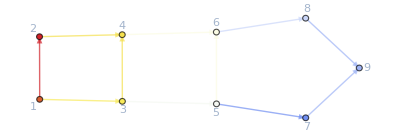

```mathematica
ColorNetworkByValueFunctionOperator[d2e][result]
```

```mathematica
d2e=D2E[Data/.{I1-> 2,I2->6, U1-> 1,U2->2,U3->0}];
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

1.9647

```mathematica
{time,d2e}=AbsoluteTiming@D2E[Data/.{I1-> 2.00000000001515151515151515115151515115151515151551515151,I2->6, U1-> 3,U2->3,U3->0.}];
time
{time,{system,rules}}=CriticalCongestionSolver[d2e]//AbsoluteTiming;
time
```

0.102996

2.26777

#### Non-linear case

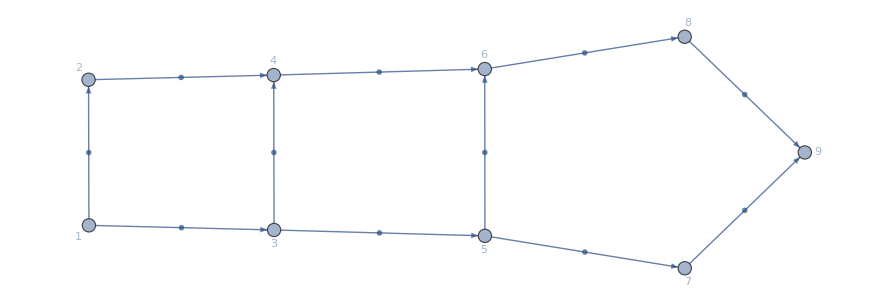

-Graphics-

```mathematica
(*Don't forget to change the Range!*)
alpha =1;
MFGEquations = d2e;
FFR=rules;
BEL=EdgeList[MFGEquations["BG"]];
pop=(#-> Plot[M[MFGEquations["jays"][#]/.FFR,x,#],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,2.4},*)GridLines->Automatic,ImageSize->90])&/@BEL;
val=(#-> Plot[U[x, #, MFGEquations/.FFR],{x,0,1}, (*PlotLabel->#,*)(*PlotRange->{-0.1,4.7},*)GridLines->Automatic,ImageSize->90])&/@BEL;
Graph[MFGEquations["BG"],EdgeLabels-> pop,GraphLayout->"SpringElectricalEmbedding"]
Graph[MFGEquations["BG"],EdgeLabels-> val,GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Solver[d2e][alpha = .1]
(*{timeFFR,FFR}= AbsoluteTiming[Catch@FixedPoint[FixedReduceX1[d2e1],rules1,200]//N//KeySort]*)
```

### The nonlinear solver solves the critical congestion case when the alpha is 1 and the initial currents are all zero.

```mathematica
rules0=AssociationThread[Values@d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]]
```

```mathematica
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
```

```mathematica
rules0=AssociationThread[Values @ d2e["jvars"],Table[0,{i,1,Length@d2e["jvars"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@KeySort@Catch@FixedPoint[FixedReduceX1[d2e],rules0, 1]
d2e["EqCriticalCase"]/.FFR
```

### Test on a “large” network

#### D2E already takes half a minute. Set the option of giving the Graph with GridGraph, for example. Would this run faster?

length of system: 238

number of alernatives: 80

length of system after eliminating us: 232

new number of alernatives: 76

CCS:
j1≥0&&j2≥0&&8/7+j29≥0&&6/7+j30≥0&&4/7+j31≥0&&4/7+j32≥0&&4/7+j31≥0&&6/7+j34≥0&&8/7+j35≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j16≥0&&j23≥0&&j24≥0&&-2+j1≥0&&-2+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j31≥0&&j34≥0&&j35≥0&&-6/7+j10≥0&&-6/7+j11≥0&&-4/7+j12≥0&&-6/7+j13≥0&&-8/7+j14≥0&&-4/7+j15≥0&&-4/7+j16≥0&&-6/7+j17≥0&&-4/7+j18≥0&&-6/7+j19≥0&&-6/7+j20≥0&&-2+j21≥0&&-4/7+j16≥0&&-8/7+j23≥0&&-2+j24≥0&&-2+j1≥0&&-2+j2≥0&&2+j1-j2≥0&&2-j1+j2≥0&&-6/7+j1-j30+jt10≥0&&6/7+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-2+j1-j29+jt10≥0&&2-j1+j29+j30-jt10≥0&&jt13≥0&&8/7+j29-jt13≥0&&4/7+j29+j31-j32-jt13≥0&&-4/7-j29+j32+jt13≥0&&-4/7-j31+j32+jt13≥0&&4/7+j31-jt13≥0&&4/7+j31≥0&&j31≥0&&jt21≥0&&j2-jt21≥0&&-8/7+j2+j34-j35-jt21≥0&&8/7-j2+j35+jt21≥0&&-6/7-j34+j35+jt21≥0&&6/7+j34-jt21≥0&&jt27≥0&&jt28≥0&&6/7+j30-jt27-jt28≥0&&jt30≥0&&jt31≥0&&6/7+j34-jt30-jt31≥0&&jt33≥0&&6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33≥0&&-12/7+j11-j30-j34+jt27+jt28+jt30+jt31≥0&&j30-jt30-jt33≥0&&-6/7-j10+j11-j30+jt28+jt30+jt31+jt33≥0&&j10-jt28-jt31≥0&&jt39≥0&&jt40≥0&&4/7+j32-jt39-jt40≥0&&jt42≥0&&jt43≥0&&j10-jt42-jt43≥0&&jt45≥0&&j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45≥0&&-4/7-j10+j13-j32+jt39+jt40+jt42+jt43≥0&&j32-jt42-jt45≥0&&-6/7-j12+j13-j32+jt40+jt42+jt43+jt45≥0&&j12-jt40-jt43≥0&&jt51≥0&&4/7+j31-jt51≥0&&4/7+j12-j14+j31-jt51≥0&&-4/7+j14-j31+jt51≥0&&-4/7-j12+j14+jt51≥0&&-4/7+j12-jt51≥0&&jt57≥0&&8/7+j35-jt57≥0&&4/7+j15-j16+j35-jt57≥0&&-8/7+j16-j35+jt57≥0&&-4/7-j15+j16+jt57≥0&&j15-jt57≥0&&jt63≥0&&jt64≥0&&j11-jt63-jt64≥0&&jt66≥0&&jt67≥0&&j15-jt66-jt67≥0&&jt69≥0&&-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69≥0&&-j11-j15+j18+jt63+jt64+jt66+jt67≥0&&-6/7+j11-jt66-jt69≥0&&2/7-j11-j17+j18+jt64+jt66+jt67+jt69≥0&&j17-jt64-jt67≥0&&jt75≥0&&jt76≥0&&j13-jt75-jt76≥0&&jt78≥0&&jt79≥0&&j17-jt78-jt79≥0&&jt81≥0&&-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81≥0&&-j13-j17+j20+jt75+jt76+jt78+jt79≥0&&-6/7+j13-jt78-jt81≥0&&-j13-j19+j20+jt76+jt78+jt79+jt81≥0&&j19-jt76-jt79≥0&&jt87≥0&&j14-jt87≥0&&j14+j19-j21-jt87≥0&&-j14+j21+jt87≥0&&-8/7-j19+j21+jt87≥0&&-6/7+j19-jt87≥0&&j16≥0&&-4/7+j16≥0&&-4/7+j16-jt100≥0&&4/7-j16+j18+jt100≥0&&4/7+j18-j23+jt100≥0&&-4/7+j16-j18+j23-jt100≥0&&-8/7+j23-jt100≥0&&jt100≥0&&jt101≥0&&j20-jt101≥0&&j20+j23-j24-jt101≥0&&-j20+j24+jt101≥0&&-6/7-j23+j24+jt101≥0&&-8/7+j23-jt101≥0&&-2+j24≥0&&2+j21-j24≥0&&-2+j21≥0&&2-j21+j24≥0&&(-2+j1==0||j1==0)&&(-2+j2==0||j2==0)&&(j29==0||8/7+j29==0)&&(j30==0||6/7+j30==0)&&(j31==0||4/7+j31==0)&&(j32==0||4/7+j32==0)&&(j31==0||4/7+j31==0)&&(j34==0||6/7+j34==0)&&(j35==0||8/7+j35==0)&&(-6/7+j10==0||j10==0)&&(-6/7+j11==0||j11==0)&&(-4/7+j12==0||j12==0)&&(-6/7+j13==0||j13==0)&&(-8/7+j14==0||j14==0)&&(-4/7+j15==0||j15==0)&&(-4/7+j16==0||j16==0)&&(-6/7+j17==0||j17==0)&&(-4/7+j18==0||j18==0)&&(-6/7+j19==0||j19==0)&&(-6/7+j20==0||j20==0)&&(-2+j21==0||j21==0)&&(-4/7+j16==0||j16==0)&&(-8/7+j23==0||j23==0)&&(-2+j24==0||j24==0)&&(-2+j1==0||-2+j2==0)&&(jt10==0||2-j1+j29+j30-jt10==0)&&(jt100==0||-4/7+j16-j18+j23-jt100==0)&&(jt101==0||j20+j23-j24-jt101==0)&&(j20-jt101==0||-6/7-j23+j24+jt101==0)&&(-j20+j24+jt101==0||-8/7+j23-jt101==0)&&(-2+j24==0||-2+j21==0)&&(-2+j1-j29+jt10==0||6/7+j30-jt10==0)&&(jt13==0||4/7+j29+j31-j32-jt13==0)&&(8/7+j29-jt13==0||-4/7-j31+j32+jt13==0)&&(-4/7-j29+j32+jt13==0||4/7+j31-jt13==0)&&(4/7+j31==0||j31==0)&&(jt21==0||-8/7+j2+j34-j35-jt21==0)&&(j2-jt21==0||-6/7-j34+j35+jt21==0)&&(8/7-j2+j35+jt21==0||6/7+j34-jt21==0)&&(jt27==0||jt30==0)&&(jt28==0||jt33==0)&&(6/7+j30-jt27-jt28==0||j30-jt30-jt33==0)&&(jt31==0||6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33==0)&&(6/7+j34-jt30-jt31==0||-6/7-j10+j11-j30+jt28+jt30+jt31+jt33==0)&&(-12/7+j11-j30-j34+jt27+jt28+jt30+jt31==0||j10-jt28-jt31==0)&&(jt39==0||jt42==0)&&(jt40==0||jt45==0)&&(4/7+j32-jt39-jt40==0||j32-jt42-jt45==0)&&(jt43==0||j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45==0)&&(j10-jt42-jt43==0||-6/7-j12+j13-j32+jt40+jt42+jt43+jt45==0)&&(-4/7-j10+j13-j32+jt39+jt40+jt42+jt43==0||j12-jt40-jt43==0)&&(jt51==0||4/7+j12-j14+j31-jt51==0)&&(4/7+j31-jt51==0||-4/7-j12+j14+jt51==0)&&(-4/7+j14-j31+jt51==0||-4/7+j12-jt51==0)&&(jt57==0||4/7+j15-j16+j35-jt57==0)&&(8/7+j35-jt57==0||-4/7-j15+j16+jt57==0)&&(-8/7+j16-j35+jt57==0||j15-jt57==0)&&(jt63==0||jt66==0)&&(jt64==0||jt69==0)&&(j11-jt63-jt64==0||-6/7+j11-jt66-jt69==0)&&(jt67==0||-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69==0)&&(j15-jt66-jt67==0||2/7-j11-j17+j18+jt64+jt66+jt67+jt69==0)&&(-6/7+j1-j30+jt10==0||j29-jt10==0)&&(-j11-j15+j18+jt63+jt64+jt66+jt67==0||j17-jt64-jt67==0)&&(jt75==0||jt78==0)&&(jt76==0||jt81==0)&&(j13-jt75-jt76==0||-6/7+j13-jt78-jt81==0)&&(jt79==0||-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81==0)&&(j17-jt78-jt79==0||-j13-j19+j20+jt76+jt78+jt79+jt81==0)&&(-j13-j17+j20+jt75+jt76+jt78+jt79==0||j19-jt76-jt79==0)&&(jt87==0||j14+j19-j21-jt87==0)&&(j14-jt87==0||-8/7-j19+j21+jt87==0)&&(-j14+j21+jt87==0||-6/7+j19-jt87==0)&&(j16==0||-4/7+j16==0)&&(-4/7+j16-jt100==0||4/7+j18-j23+jt100==0)&&(4/7-j16+j18+jt100==0||-8/7+j23-jt100==0)

CCS:
((7 jt79==6&&((jt76==0&&(jt81==0||jt81==0))||(jt76==0&&jt81==0)))||(jt81==0&&((7 jt76==6&&(jt79==0||jt79==0))||(7 jt76≤6&&jt76≥0&&jt76+jt79==6/7))))&&((jt40==0&&7 jt43==4&&(jt45==0||jt45==0))||(jt45==0&&((7 jt40==4&&(jt43==0||jt43==0))||(7 jt40≤4&&jt40≥0&&jt40+jt43==4/7))))&&((7 jt64==6&&(jt67==0||jt67==0))||(jt64==2/7&&7 jt67==4)||(7 jt64≤6&&7 jt64≥2&&jt64+jt67==6/7))&&((7 jt31==6&&((jt28==0&&(jt33==0||jt33==0))||(jt28==0&&jt33==0)))||(jt33==0&&((7 jt28==6&&(jt31==0||jt31==0))||(7 jt28≤6&&jt28≥0&&jt28+jt31==6/7))))

CCS:
((jt28==0&&7 jt31==6)||(7 jt28==6&&jt31==0)||(7 jt28≤6&&jt28≥0&&jt28+jt31==6/7))&&((jt40==0&&7 jt43==4)||(7 jt40==4&&jt43==0)||(7 jt40≤4&&jt40≥0&&jt40+jt43==4/7))&&((7 jt64==6&&jt67==0)||(7 jt64==2&&7 jt67==4)||(7 jt64≤6&&7 jt64≥2&&jt64+jt67==6/7))&&((jt76==0&&7 jt79==6)||(7 jt76==6&&jt79==0)||(7 jt76≤6&&jt76≥0&&jt76+jt79==6/7))

55.5666

0≤jt79≤6/7&&jt76==1/7 (6-7 jt79)&&0≤jt67≤4/7&&jt64==1/7 (6-7 jt67)&&0≤jt43≤4/7&&jt40==1/7 (4-7 jt43)&&0≤jt31≤6/7&&jt28==1/7 (6-7 jt31)

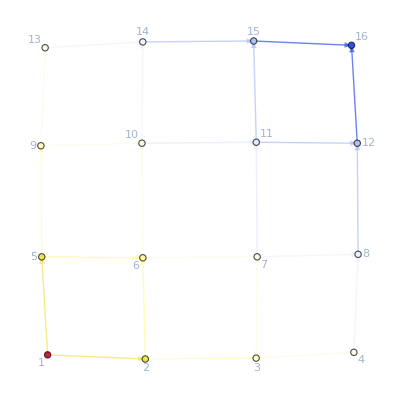

```mathematica
eme=4;
ege=4;
ete =1;
gr=GridGraph[{eme,ege,ete},DirectedEdges->True];
{timegridata,d2egrid}=AbsoluteTiming@D2E[
AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0},(*SwitchingCostsData=*){}}]
];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
systemgrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Solve//FindInstance
```

FindInstance[{{jt28→ConditionalExpression[1/7 (6-7 jt31), 0≤jt31≤6/7],jt40→ConditionalExpression[1/7 (4-7 jt43), 0≤jt43≤4/7],jt64→ConditionalExpression[1/7 (6-7 jt67), 0≤jt67≤4/7],jt76→ConditionalExpression[1/7 (6-7 jt79), 0≤jt79≤6/7]}}]

```mathematica
Manipulate[eme=2;
ege=3;
ete =1;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege*ete,U1}/.U1->0, {eme*ege*ete-1,0}, {eme*ege*ete-2,U2}},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print[timegrid];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid],{{U2,100},0,1000,10}]
```

length of system: 231

number of alernatives: 78

length of system after eliminating us: 214

new number of alernatives: 68

CCS:
j1≥0&&j2≥0&&1973600/14101+j29≥0&&1050900/14101+j30≥0&&1239200/14101+j31≥0&&734400/14101+j32≥0&&558400/14101+j33≥0&&680800/14101+j34≥0&&558400/14101+j33≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j11≥0&&j20≥0&&j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j33≥0&&-1459500/14101+j10≥0&&-19600/239+j11≥0&&-1657100/14101+j12≥0&&-853300/14101+j13≥0&&-1185600/14101+j14≥0&&-1205900/14101+j15≥0&&-436000/14101+j16≥0&&-1430400/14101+j17≥0&&-994400/14101+j18≥0&&-19600/239+j11≥0&&-2009700/14101+j20≥0&&-100+j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&jt13≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&jt19≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&jt27≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&jt33≥0&&jt34≥0&&1050900/14101+j30-jt33-jt34≥0&&jt36≥0&&jt37≥0&&j10-jt36-jt37≥0&&jt39≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&jt45≥0&&jt46≥0&&734400/14101+j32-jt45-jt46≥0&&jt48≥0&&jt49≥0&&j12-jt48-jt49≥0&&jt51≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&jt57≥0&&jt58≥0&&680800/14101+j34-jt57-jt58≥0&&jt60≥0&&jt61≥0&&j14-jt60-jt61≥0&&jt63≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&jt69≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&j11≥0&&-19600/239+j11≥0&&jt77≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&jt83≥0&&jt84≥0&&j15-jt83-jt84≥0&&jt86≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&-1205900/14101+j15-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&jt100≥0&&jt101≥0&&jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-3024500/14101+j1==0||j1==0)&&(-2615900/14101+j2==0||j2==0)&&(j29==0||1973600/14101+j29==0)&&(j30==0||1050900/14101+j30==0)&&(j31==0||1239200/14101+j31==0)&&(j32==0||734400/14101+j32==0)&&(j33==0||558400/14101+j33==0)&&(j34==0||680800/14101+j34==0)&&(j33==0||558400/14101+j33==0)&&(-1459500/14101+j10==0||j10==0)&&(-19600/239+j11==0||j11==0)&&(-1657100/14101+j12==0||j12==0)&&(-853300/14101+j13==0||j13==0)&&(-1185600/14101+j14==0||j14==0)&&(-1205900/14101+j15==0||j15==0)&&(-436000/14101+j16==0||j16==0)&&(-1430400/14101+j17==0||j17==0)&&(-994400/14101+j18==0||j18==0)&&(-19600/239+j11==0||j11==0)&&(-2009700/14101+j20==0||j20==0)&&(-100+j21==0||j21==0)&&(j23==0||j23==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j23==0||-994400/14101+j18==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt57==0||jt60==0)&&(jt58==0||jt63==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(jt83==0||jt86==0)&&(jt84==0||-1205900/14101+j15-jt86==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0)

CCS:
14101 jt84≤1205900&&jt84≥0&&((jt58==0&&14101 jt61==436000&&(jt63==0||jt63==0))||(jt63==0&&((14101 jt58==436000&&jt61==0)||(14101 jt58≤436000&&jt58≥0&&jt58+jt61==436000/14101))))&&((14101 jt34==1050900&&jt37==606200/14101)||(jt34==197600/14101&&14101 jt37==1459500)||(14101 jt34≤1050900&&14101 jt34≥197600&&jt34+jt37==1657100/14101))&&((jt46==0&&14101 jt49==1185600&&(jt51==0||jt51==0))||(jt51==0&&((14101 jt46==734400&&jt49==451200/14101)||(14101 jt46≤734400&&jt46≥0&&jt46+jt49==1185600/14101))))&&(100==100+jt101||jt101==0)

CCS:
14101 jt84≤1205900&&jt84≥0&&((jt46==0&&14101 jt49==1185600)||(14101 jt46==734400&&14101 jt49==451200)||(jt46+jt49==1185600/14101&&jt46≥0&&14101 jt46≤734400))&&((14101 jt34==1050900&&14101 jt37==606200)||(14101 jt34==197600&&14101 jt37==1459500)||(jt34+jt37==1657100/14101&&14101 jt34≥197600&&14101 jt34≤1050900))&&((jt58==0&&14101 jt61==436000)||(14101 jt58==436000&&jt61==0)||(14101 jt58≤436000&&jt58≥0&&jt58+jt61==436000/14101))

21.1794

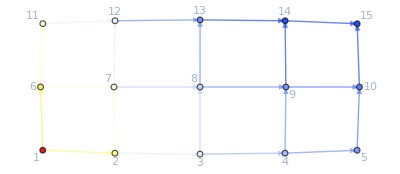

```mathematica
eme=5;
ege=3;
gr=GridGraph[{eme,ege},DirectedEdges->True];
Datagrid =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->400},(*FinalCosts=*){{eme*ege,U1}/.U1->0, {eme*ege-1,0}, {eme*ege-2,U2}/.U2->100},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Datagrid];
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
Print["It took ",timegrid, " seconds to solve the critical congestion case."];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
systemgrid//Reduce[#,Reals]&
```

0≤jt61≤436000/14101&&jt58==(436000-14101 jt61)/14101&&451200/14101≤jt49≤1185600/14101&&jt46==(1185600-14101 jt49)/14101&&606200/14101≤jt37≤1459500/14101&&jt34==(1657100-14101 jt37)/14101&&0≤jt84≤1205900/14101

The error (1-Norm of LHS-RHS) is 9.9476×10^-13

The error is 9.9476×10^-13 which is less than 1.×10^-10

It took 3.79549 seconds to solve!
	The system is 200/7≤jt16≤100

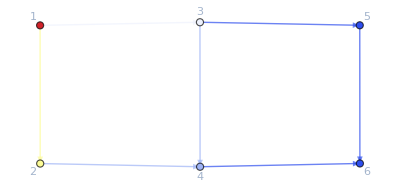

```mathematica
rulesgridsolver = Solver[d2egrid][alpha=1];
ColorNetworkByValueFunctionOperator[d2egrid][rulesgridsolver]
```

```mathematica
gr=GridGraph[{3,7},DirectedEdges->True, VertexLabels->"Name"];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{8,I1}/.I1->400},(*FinalCosts=*){{17,U1}/.U1->0},(*SwitchingCostsData=*){}}];
```

```mathematica
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data]
```

```mathematica
d2egrid["EqAllAll"]
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=CriticalCongestionSolver[d2egrid]//AbsoluteTiming;
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
gr=GridGraph[{3,3},DirectedEdges->True];
Data =AssociationThread[{"Vertices List","Adjacency Matrix","Entrance Vertices and Currents","Exit Vertices and Terminal Costs","Switching Costs"}, {(*VL=*)VertexList[gr],(*AM=*)AdjacencyMatrix[gr],(*DataIn=*){{1,I1}/.I1->4,{3,4}},(*FinalCosts=*){{5,U1}/.U1->0(*,{8,0}*)},(*SwitchingCostsData=*){}}];
{timegridata,d2egrid}=AbsoluteTiming@D2E[Data];
alpha=1;
(rulesgrid = Solver[d2egrid][alpha]);
```

```mathematica
{timegrid,{systemgrid,rulesgrid}}=AbsoluteTiming@CriticalCongestionSolver[d2egrid];
timegrid
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rulesgrid=KeySort@rulesgrid;
ColorNetworkByValueFunctionOperator[d2egrid][rulesgrid]
```

```mathematica
rules0=AssociationThread[d2egrid["js"],Table[0,{i,1,Length@d2egrid["js"]}]];
alpha = 1;
{timeFFR,FFR}= AbsoluteTiming@Catch@FixedPoint[FixedReduceX1[d2egrid],rules0, 1]
d2egrid["EqCriticalCase"]/.FFR
```

# TestZone

```mathematica
EqAllAll=Lookup[d2egrid,"EqAllAll",Print["No equations to solve."];
Return[]];
EqCriticalCase=Lookup[d2egrid,"EqCriticalCase",Print["Critical case equations are missing."];
Return[]];
InitRules=Lookup[d2egrid,"BoundaryRules",Print["Need boundary conditions"];];
```

```mathematica
{system,rules}=CleanEqualities[{EqCriticalCase&&EqAllAll,InitRules}];
```

```mathematica
Keys[d2egrid]
```

{Vertices List,Adjacency Matrix,Entrance Vertices and Currents,Exit Vertices and Terminal Costs,Switching Costs,BG,FG,jvars,jtvars,uvars,OutRules,InRules,jays,ExitCosts,AllOr,AllEq,AllIneq,EqAllAll,BoundaryRules,Nlhs,MinimalTimeRhs,EqCriticalCase,Nrhs}

```mathematica
Length[d2egrid["AllEq"]]
Length[d2egrid["AllEq"]/.rules]
Length[d2egrid["AllOr"]]
Length[d2egrid["AllOr"]/.rules]
Length[d2egrid["AllIneq"]]
Length[d2egrid["AllIneq"]/.rules]
Length[d2egrid["EqCriticalCase"]]
Length[d2egrid["EqCriticalCase"]/.rules]
```

#### This is the winning code!

```mathematica
{system,rules}=((And@@(NewReduce/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["uvars"]]))//Simplify)&&system)//CleanEqualities
```

{j1≥0&&j2≥0&&1973600/14101+j29≥0&&1050900/14101+j30≥0&&1239200/14101+j31≥0&&734400/14101+j32≥0&&558400/14101+j33≥0&&680800/14101+j34≥0&&558400/14101+j33≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j11≥0&&j20≥0&&j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j33≥0&&j34≥0&&j33≥0&&-1459500/14101+j10≥0&&-19600/239+j11≥0&&-1657100/14101+j12≥0&&-853300/14101+j13≥0&&-1185600/14101+j14≥0&&-1205900/14101+j15≥0&&-436000/14101+j16≥0&&-1430400/14101+j17≥0&&-994400/14101+j18≥0&&-19600/239+j11≥0&&-2009700/14101+j20≥0&&-100+j21≥0&&j23≥0&&-3024500/14101+j1≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&jt13≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&jt19≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&jt27≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&jt33≥0&&jt34≥0&&1050900/14101+j30-jt33-jt34≥0&&jt36≥0&&jt37≥0&&j10-jt36-jt37≥0&&jt39≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&jt45≥0&&jt46≥0&&734400/14101+j32-jt45-jt46≥0&&jt48≥0&&jt49≥0&&j12-jt48-jt49≥0&&jt51≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&jt57≥0&&jt58≥0&&680800/14101+j34-jt57-jt58≥0&&jt60≥0&&jt61≥0&&j14-jt60-jt61≥0&&jt63≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&jt69≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&j11≥0&&-19600/239+j11≥0&&jt77≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&jt83≥0&&jt84≥0&&j15-jt83-jt84≥0&&jt86≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&-1205900/14101+j15-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&jt100≥0&&jt101≥0&&jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-3024500/14101+j1==0||j1==0)&&(-2615900/14101+j2==0||j2==0)&&(j29==0||1973600/14101+j29==0)&&(j30==0||1050900/14101+j30==0)&&(j31==0||1239200/14101+j31==0)&&(j32==0||734400/14101+j32==0)&&(j33==0||558400/14101+j33==0)&&(j34==0||680800/14101+j34==0)&&(j33==0||558400/14101+j33==0)&&(-1459500/14101+j10==0||j10==0)&&(-19600/239+j11==0||j11==0)&&(-1657100/14101+j12==0||j12==0)&&(-853300/14101+j13==0||j13==0)&&(-1185600/14101+j14==0||j14==0)&&(-1205900/14101+j15==0||j15==0)&&(-436000/14101+j16==0||j16==0)&&(-1430400/14101+j17==0||j17==0)&&(-994400/14101+j18==0||j18==0)&&(-19600/239+j11==0||j11==0)&&(-2009700/14101+j20==0||j20==0)&&(-100+j21==0||j21==0)&&(j23==0||j23==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j23==0||-994400/14101+j18==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt33==0||jt36==0)&&(jt34==0||jt39==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt45==0||jt48==0)&&(jt46==0||jt51==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt57==0||jt60==0)&&(jt58==0||jt63==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(jt83==0||jt86==0)&&(jt84==0||-1205900/14101+j15-jt86==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),<|j22→1805500/14101,j24→2840500/14101,u1→141500/239,u26→141500/239|>}

```mathematica
Head/@system
```

GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&GreaterEqual&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or&&Or

```mathematica
Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jvars"]]
```

{j1≥0&&-3024500/14101+j1≥0&&-3024500/14101+j1≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&-1050900/14101+j1-j30+jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&(-3024500/14101+j1==0||j1==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),j2≥0&&-2615900/14101+j2≥0&&-2615900/14101+j2≥0&&2615900/14101+j1-j2≥0&&3024500/14101-j1+j2≥0&&j2-jt27≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&(-2615900/14101+j2==0||j2==0)&&(-3024500/14101+j1==0||-2615900/14101+j2==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0),True,True,True,True,True,True,True,j10≥0&&-1459500/14101+j10≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&-19600/239-j10+j11+jt27≥0&&j10-jt27≥0&&j10-jt36-jt37≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&(-1459500/14101+j10==0||j10==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0),j11≥0&&j11≥0&&-19600/239+j11≥0&&-19600/239+j11≥0&&-1459500/14101+j10-j11+j2-jt27≥0&&j11-j2+jt27≥0&&-19600/239-j10+j11+jt27≥0&&j11≥0&&-19600/239+j11≥0&&j11+j13-j20-jt77≥0&&-853300/14101-j11+j20+jt77≥0&&-19600/239+j11-jt77≥0&&(-19600/239+j11==0||j11==0)&&(-19600/239+j11==0||j11==0)&&(jt27==0||-1459500/14101+j10-j11+j2-jt27==0)&&(j2-jt27==0||-19600/239-j10+j11+jt27==0)&&(j11-j2+jt27==0||j10-jt27==0)&&(j11==0||-19600/239+j11==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0),j12≥0&&-1657100/14101+j12≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j12-jt34-jt37≥0&&j12-jt48-jt49≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&(-1657100/14101+j12==0||j12==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0),j13≥0&&-853300/14101+j13≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&j13-jt77≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&(-853300/14101+j13==0||j13==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0),j14≥0&&-1185600/14101+j14≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j14-jt46-jt49≥0&&j14-jt60-jt61≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&(-1185600/14101+j14==0||j14==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0),j15≥0&&-1205900/14101+j15≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&j15-jt83-jt84≥0&&-1205900/14101+j15-jt86≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&(-1205900/14101+j15==0||j15==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0)&&(jt84==0||-1205900/14101+j15-jt86==0),j16≥0&&-436000/14101+j16≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&j16-jt58-jt61≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101-j16+j18+jt69≥0&&-436000/14101+j16-jt69≥0&&(-436000/14101+j16==0||j16==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),j17≥0&&-1430400/14101+j17≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&-1430400/14101+j17-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&(-1430400/14101+j17==0||j17==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),j18≥0&&-994400/14101+j18≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&-558400/14101-j16+j18+jt69≥0&&j18-j23≥0&&-994400/14101+j18≥0&&994400/14101-j18+j23≥0&&(-994400/14101+j18==0||j18==0)&&(j23==0||-994400/14101+j18==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),True,j20≥0&&-2009700/14101+j20≥0&&j11+j13-j20-jt77≥0&&-j13+j20+jt77≥0&&-853300/14101-j11+j20+jt77≥0&&j20-j21+jt84-jt86≥0&&-2009700/14101+j20-jt83≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&(-2009700/14101+j20==0||j20==0)&&(jt77==0||j11+j13-j20-jt77==0)&&(j13-jt77==0||-853300/14101-j11+j20+jt77==0)&&(-j13+j20+jt77==0||-19600/239+j11-jt77==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0),j21≥0&&-100+j21≥0&&j21-jt84≥0&&j20-j21+jt84-jt86≥0&&1805500/14101-j15-j20+j21+jt83+jt86≥0&&-100+j21-jt102≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&1430400/14101-j17+j21-jt100+jt101≥0&&(-100+j21==0||j21==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(jt102==0||1430400/14101-j17+j21-jt100+jt101==0)&&(j21-jt84==0||-2009700/14101+j20-jt83==0)&&(-100+j21-jt102==0||-1430400/14101+j17-jt101==0),True,j23≥0&&j23≥0&&-1430400/14101+j17-j21+j23+jt100-jt101≥0&&2840500/14101-j23-jt100+jt101+jt102≥0&&j23-jt101-jt102≥0&&j23≥0&&j18-j23≥0&&994400/14101-j18+j23≥0&&(j23==0||j23==0)&&(jt101==0||-1430400/14101+j17-j21+j23+jt100-jt101==0)&&(j23==0||-994400/14101+j18==0),True,True,True,True,True,1973600/14101+j29≥0&&j29≥0&&j29-jt10≥0&&-3024500/14101+j1-j29+jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&1973600/14101+j29-jt13≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&(j29==0||1973600/14101+j29==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),1050900/14101+j30≥0&&j30≥0&&-1050900/14101+j1-j30+jt10≥0&&1050900/14101+j30-jt10≥0&&3024500/14101-j1+j29+j30-jt10≥0&&1050900/14101+j30-jt33-jt34≥0&&-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39≥0&&-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37≥0&&j30-jt36-jt39≥0&&-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39≥0&&(j30==0||1050900/14101+j30==0)&&(jt10==0||3024500/14101-j1+j29+j30-jt10==0)&&(-3024500/14101+j1-j29+jt10==0||1050900/14101+j30-jt10==0)&&(1050900/14101+j30-jt33-jt34==0||j30-jt36-jt39==0)&&(jt37==0||-606200/14101+j10+j12-j13+j30-jt33-jt34-jt36-jt37-jt39==0)&&(j10-jt36-jt37==0||-853300/14101-j12+j13-j30+jt34+jt36+jt37+jt39==0)&&(-1050900/14101-j10+j13-j30+jt33+jt34+jt36+jt37==0||j12-jt34-jt37==0)&&(-1050900/14101+j1-j30+jt10==0||j29-jt10==0),1239200/14101+j31≥0&&j31≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&1239200/14101+j31-jt13≥0&&1239200/14101+j31-jt19≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&(j31==0||1239200/14101+j31==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0),734400/14101+j32≥0&&j32≥0&&1239200/14101+j29+j31-j32-jt13≥0&&-1239200/14101-j29+j32+jt13≥0&&-1239200/14101-j31+j32+jt13≥0&&734400/14101+j32-jt45-jt46≥0&&-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51≥0&&-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49≥0&&j32-jt48-jt51≥0&&-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51≥0&&(j32==0||734400/14101+j32==0)&&(jt13==0||1239200/14101+j29+j31-j32-jt13==0)&&(1973600/14101+j29-jt13==0||-1239200/14101-j31+j32+jt13==0)&&(-1239200/14101-j29+j32+jt13==0||1239200/14101+j31-jt13==0)&&(734400/14101+j32-jt45-jt46==0||j32-jt48-jt51==0)&&(jt49==0||-451200/14101+j12+j14-j15+j32-jt45-jt46-jt48-jt49-jt51==0)&&(j12-jt48-jt49==0||-1205900/14101-j14+j15-j32+jt46+jt48+jt49+jt51==0)&&(-734400/14101-j12+j15-j32+jt45+jt46+jt48+jt49==0||j14-jt46-jt49==0),558400/14101+j33≥0&&558400/14101+j33≥0&&j33≥0&&j33≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j33+j34+jt19≥0&&558400/14101+j33-jt19≥0&&558400/14101+j33≥0&&j33≥0&&558400/14101+j33-jt69≥0&&558400/14101+j16-j18+j33-jt69≥0&&-558400/14101+j18-j33+jt69≥0&&(j33==0||558400/14101+j33==0)&&(j33==0||558400/14101+j33==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(558400/14101+j33==0||j33==0)&&(jt69==0||558400/14101+j16-j18+j33-jt69==0)&&(558400/14101+j33-jt69==0||-558400/14101-j16+j18+jt69==0)&&(-558400/14101+j18-j33+jt69==0||-436000/14101+j16-jt69==0),680800/14101+j34≥0&&j34≥0&&558400/14101+j31+j33-j34-jt19≥0&&-558400/14101-j31+j34+jt19≥0&&-558400/14101-j33+j34+jt19≥0&&680800/14101+j34-jt57-jt58≥0&&244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63≥0&&-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61≥0&&j34-jt60-jt63≥0&&-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63≥0&&(j34==0||680800/14101+j34==0)&&(jt19==0||558400/14101+j31+j33-j34-jt19==0)&&(1239200/14101+j31-jt19==0||-558400/14101-j33+j34+jt19==0)&&(-558400/14101-j31+j34+jt19==0||558400/14101+j33-jt19==0)&&(680800/14101+j34-jt57-jt58==0||j34-jt60-jt63==0)&&(jt61==0||244800/14101+j14+j16-j17+j34-jt57-jt58-jt60-jt61-jt63==0)&&(j14-jt60-jt61==0||-1430400/14101-j16+j17-j34+jt58+jt60+jt61+jt63==0)&&(-680800/14101-j14+j17-j34+jt57+jt58+jt60+jt61==0||j16-jt58-jt61==0),True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
NewReduce[And @@ (Simplify/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jtvars"]]))]
```

$Aborted

```mathematica
NewReduce[And@@(Simplify/@(Select[system,Function[a,!FreeQ[a,#]]]&/@Values[d2egrid["jtvars"]]))]
```

# This is in the code already:

### Color representation of the value function (this is suitable for the critical congestion case because the value function is linear on each edge)

#### New function!!!

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}

ColorNetworkByValueFunctionOperator[d2e1_Association][rules_]:= Module[{values,colors},
values=d2e1["VL"]/.KeyMap[#[[1]]&,d2e1["uvars"]/.rules];(*this works WITHOUT switching costs*)
(*Print[values];*)
colors=ColorData["TemperatureMap"]/@(values/Max[values]);
(*Print[colors];*)
GraphicsGrid[{
{HighlightGraph[SetProperty[d2e1["BG"],EdgeShapeFunction-> eStyle[colors]],Thread[Style[d2e1["VL"],colors]],GraphLayout->"SpringElectricalEmbedding"]},
{BarLegend["TemperatureMap",LegendMarkerSize->100,LegendLayout->"ReversedRow"]}
}]
]
```

### Idea:

```mathematica
eStyle[colors_][pts_,DirectedEdge[x_,y_]]:={colors[[y]],Arrow[Line[pts,VertexColors->{colors[[x]],colors[[y]]}]]}
g=GridGraph[{4,4},VertexLabels->"Name",ImagePadding->10,DirectedEdges->True];
colors=ColorData["TemperatureMap"]/@(VertexDegree[g]/Max[VertexDegree[g]]);
HighlightGraph[SetProperty[g,EdgeShapeFunction->eStyle[colors]],Thread[Style[VertexList[g],colors]]]
```

```mathematica
FixedPoint
```

```mathematica
system
```

j1≥0&&j2≥0&&8/7+j29≥0&&6/7+j30≥0&&4/7+j31≥0&&4/7+j32≥0&&4/7+j31≥0&&6/7+j34≥0&&8/7+j35≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j16≥0&&j23≥0&&j24≥0&&-2+j1≥0&&-2+j2≥0&&j29≥0&&j30≥0&&j31≥0&&j32≥0&&j31≥0&&j34≥0&&j35≥0&&-6/7+j10≥0&&-6/7+j11≥0&&-4/7+j12≥0&&-6/7+j13≥0&&-8/7+j14≥0&&-4/7+j15≥0&&-4/7+j16≥0&&-6/7+j17≥0&&-4/7+j18≥0&&-6/7+j19≥0&&-6/7+j20≥0&&-2+j21≥0&&-4/7+j16≥0&&-8/7+j23≥0&&-2+j24≥0&&-2+j1≥0&&-2+j2≥0&&2+j1-j2≥0&&2-j1+j2≥0&&-6/7+j1-j30+jt10≥0&&6/7+j30-jt10≥0&&j29-jt10≥0&&jt10≥0&&-2+j1-j29+jt10≥0&&2-j1+j29+j30-jt10≥0&&jt13≥0&&8/7+j29-jt13≥0&&4/7+j29+j31-j32-jt13≥0&&-4/7-j29+j32+jt13≥0&&-4/7-j31+j32+jt13≥0&&4/7+j31-jt13≥0&&4/7+j31≥0&&j31≥0&&jt21≥0&&j2-jt21≥0&&-8/7+j2+j34-j35-jt21≥0&&8/7-j2+j35+jt21≥0&&-6/7-j34+j35+jt21≥0&&6/7+j34-jt21≥0&&jt27≥0&&jt28≥0&&6/7+j30-jt27-jt28≥0&&jt30≥0&&jt31≥0&&6/7+j34-jt30-jt31≥0&&jt33≥0&&6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33≥0&&-12/7+j11-j30-j34+jt27+jt28+jt30+jt31≥0&&j30-jt30-jt33≥0&&-6/7-j10+j11-j30+jt28+jt30+jt31+jt33≥0&&j10-jt28-jt31≥0&&jt39≥0&&jt40≥0&&4/7+j32-jt39-jt40≥0&&jt42≥0&&jt43≥0&&j10-jt42-jt43≥0&&jt45≥0&&j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45≥0&&-4/7-j10+j13-j32+jt39+jt40+jt42+jt43≥0&&j32-jt42-jt45≥0&&-6/7-j12+j13-j32+jt40+jt42+jt43+jt45≥0&&j12-jt40-jt43≥0&&jt51≥0&&4/7+j31-jt51≥0&&4/7+j12-j14+j31-jt51≥0&&-4/7+j14-j31+jt51≥0&&-4/7-j12+j14+jt51≥0&&-4/7+j12-jt51≥0&&jt57≥0&&8/7+j35-jt57≥0&&4/7+j15-j16+j35-jt57≥0&&-8/7+j16-j35+jt57≥0&&-4/7-j15+j16+jt57≥0&&j15-jt57≥0&&jt63≥0&&jt64≥0&&j11-jt63-jt64≥0&&jt66≥0&&jt67≥0&&j15-jt66-jt67≥0&&jt69≥0&&-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69≥0&&-j11-j15+j18+jt63+jt64+jt66+jt67≥0&&-6/7+j11-jt66-jt69≥0&&2/7-j11-j17+j18+jt64+jt66+jt67+jt69≥0&&j17-jt64-jt67≥0&&jt75≥0&&jt76≥0&&j13-jt75-jt76≥0&&jt78≥0&&jt79≥0&&j17-jt78-jt79≥0&&jt81≥0&&-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81≥0&&-j13-j17+j20+jt75+jt76+jt78+jt79≥0&&-6/7+j13-jt78-jt81≥0&&-j13-j19+j20+jt76+jt78+jt79+jt81≥0&&j19-jt76-jt79≥0&&jt87≥0&&j14-jt87≥0&&j14+j19-j21-jt87≥0&&-j14+j21+jt87≥0&&-8/7-j19+j21+jt87≥0&&-6/7+j19-jt87≥0&&j16≥0&&-4/7+j16≥0&&-4/7+j16-jt100≥0&&4/7-j16+j18+jt100≥0&&4/7+j18-j23+jt100≥0&&-4/7+j16-j18+j23-jt100≥0&&-8/7+j23-jt100≥0&&jt100≥0&&jt101≥0&&j20-jt101≥0&&j20+j23-j24-jt101≥0&&-j20+j24+jt101≥0&&-6/7-j23+j24+jt101≥0&&-8/7+j23-jt101≥0&&-2+j24≥0&&2+j21-j24≥0&&-2+j21≥0&&2-j21+j24≥0&&u1≥u26&&0≥-52/7+u1&&(-2+j1==0||j1==0)&&(-2+j2==0||j2==0)&&(j29==0||8/7+j29==0)&&(j30==0||6/7+j30==0)&&(j31==0||4/7+j31==0)&&(j32==0||4/7+j32==0)&&(j31==0||4/7+j31==0)&&(j34==0||6/7+j34==0)&&(j35==0||8/7+j35==0)&&(-6/7+j10==0||j10==0)&&(-6/7+j11==0||j11==0)&&(-4/7+j12==0||j12==0)&&(-6/7+j13==0||j13==0)&&(-8/7+j14==0||j14==0)&&(-4/7+j15==0||j15==0)&&(-4/7+j16==0||j16==0)&&(-6/7+j17==0||j17==0)&&(-4/7+j18==0||j18==0)&&(-6/7+j19==0||j19==0)&&(-6/7+j20==0||j20==0)&&(-2+j21==0||j21==0)&&(-4/7+j16==0||j16==0)&&(-8/7+j23==0||j23==0)&&(-2+j24==0||j24==0)&&(-2+j1==0||-2+j2==0)&&(jt10==0||2-j1+j29+j30-jt10==0)&&(jt100==0||-4/7+j16-j18+j23-jt100==0)&&(jt101==0||j20+j23-j24-jt101==0)&&(j20-jt101==0||-6/7-j23+j24+jt101==0)&&(-j20+j24+jt101==0||-8/7+j23-jt101==0)&&(-2+j24==0||-2+j21==0)&&(-2+j1-j29+jt10==0||6/7+j30-jt10==0)&&(jt13==0||4/7+j29+j31-j32-jt13==0)&&(8/7+j29-jt13==0||-4/7-j31+j32+jt13==0)&&(-4/7-j29+j32+jt13==0||4/7+j31-jt13==0)&&(4/7+j31==0||j31==0)&&(jt21==0||-8/7+j2+j34-j35-jt21==0)&&(j2-jt21==0||-6/7-j34+j35+jt21==0)&&(8/7-j2+j35+jt21==0||6/7+j34-jt21==0)&&(jt27==0||jt30==0)&&(jt28==0||jt33==0)&&(6/7+j30-jt27-jt28==0||j30-jt30-jt33==0)&&(jt31==0||6/7+j10-j11+j30+j34-jt27-jt28-jt30-jt31-jt33==0)&&(6/7+j34-jt30-jt31==0||-6/7-j10+j11-j30+jt28+jt30+jt31+jt33==0)&&(-12/7+j11-j30-j34+jt27+jt28+jt30+jt31==0||j10-jt28-jt31==0)&&(jt39==0||jt42==0)&&(jt40==0||jt45==0)&&(4/7+j32-jt39-jt40==0||j32-jt42-jt45==0)&&(jt43==0||j10+j12-j13+j32-jt39-jt40-jt42-jt43-jt45==0)&&(j10-jt42-jt43==0||-6/7-j12+j13-j32+jt40+jt42+jt43+jt45==0)&&(-4/7-j10+j13-j32+jt39+jt40+jt42+jt43==0||j12-jt40-jt43==0)&&(jt51==0||4/7+j12-j14+j31-jt51==0)&&(4/7+j31-jt51==0||-4/7-j12+j14+jt51==0)&&(-4/7+j14-j31+jt51==0||-4/7+j12-jt51==0)&&(jt57==0||4/7+j15-j16+j35-jt57==0)&&(8/7+j35-jt57==0||-4/7-j15+j16+jt57==0)&&(-8/7+j16-j35+jt57==0||j15-jt57==0)&&(jt63==0||jt66==0)&&(jt64==0||jt69==0)&&(j11-jt63-jt64==0||-6/7+j11-jt66-jt69==0)&&(jt67==0||-6/7+j11+j15+j17-j18-jt63-jt64-jt66-jt67-jt69==0)&&(j15-jt66-jt67==0||2/7-j11-j17+j18+jt64+jt66+jt67+jt69==0)&&(-6/7+j1-j30+jt10==0||j29-jt10==0)&&(-j11-j15+j18+jt63+jt64+jt66+jt67==0||j17-jt64-jt67==0)&&(jt75==0||jt78==0)&&(jt76==0||jt81==0)&&(j13-jt75-jt76==0||-6/7+j13-jt78-jt81==0)&&(jt79==0||-6/7+j13+j17+j19-j20-jt75-jt76-jt78-jt79-jt81==0)&&(j17-jt78-jt79==0||-j13-j19+j20+jt76+jt78+jt79+jt81==0)&&(-j13-j17+j20+jt75+jt76+jt78+jt79==0||j19-jt76-jt79==0)&&(jt87==0||j14+j19-j21-jt87==0)&&(j14-jt87==0||-8/7-j19+j21+jt87==0)&&(-j14+j21+jt87==0||-6/7+j19-jt87==0)&&(j16==0||-4/7+j16==0)&&(-4/7+j16-jt100==0||4/7+j18-j23+jt100==0)&&(4/7-j16+j18+jt100==0||-8/7+j23-jt100==0)&&(2+j1-j2==0||u1-u26==0)&&(2-j1+j2==0||u1-u26==0)&&(2+j21-j24==0||52/7-u1==0)&&(2-j21+j24==0||52/7-u1==0)

```mathematica
systemgrid
```

0≤jt79≤6/7&&jt76==1/7 (6-7 jt79)&&0≤jt67≤4/7&&jt64==1/7 (6-7 jt67)&&0≤jt43≤4/7&&jt40==1/7 (4-7 jt43)&&0≤jt31≤6/7&&jt28==1/7 (6-7 jt31)

```mathematica
FreeQ[u1][system]
And@@(FreeQ[#][system]&/@{u1,u2,u3,u4,u5})
```

False

False

```mathematica
FreeQ[#][systemgrid]&/@{u1,u2,u3,u4,u5}
```

{True,True,True,True,True}